```mathematica
s2[n_,s_]:=Sum[ j^(-1/2)(s Cosh[ s Log[n/j]]-1/2 Sinh[s Log[n/j]])/
(s Cosh[s Log[n]]+s Log[Pi]+Log[Gamma[1/2-s/2]]-Log[Gamma[1/4+s/2]]-(1/2)Sinh[s Log[n]]+s Log[Pi]+Log[Gamma[1/2-s/2]]-Log[Gamma[1/4+s/2]]),{j,1,n}]
s3[n_,s_]:=Sum[j^(-1/2)(2 s Cosh[s Log[n/j]] -Sinh[s Log[n/j]])/(2 s Cosh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]] -Sinh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]]),{j,1,n}]
s4[n_,s_]:=Sum[j^(-1/2)( s Cosh[s Log[n/j]] -(1/2)Sinh[s Log[n/j]])/( s Cosh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]] -(1/2)Sinh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]]),{j,1,n}]
s5[n_,s_]:=Sum[j^(-1/2) Cosh[s Log[n/j]-ArcCoth[2s]]/ Cosh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]-ArcCoth[2s]] ,{j,1,n}]
s5a[n_,s_]:=Sum[j^(-1/2) Cosh[s Log[n/j]-ArcCoth[2s]]/ Cosh[s Log[n]-ArcCoth[2s]] ,{j,1,n}]
s5b[n_,s_]:=Sum[j^(-1/2) Cosh[s Log[n/j]-ArcCoth[2s]]/ Cosh[s Log[n]-ArcCoth[2s]+Log[Pi^s Gamma[1/4-s/2]/Gamma[1/4+s/2]]] ,{j,1,n}]
s6[n_,s_]:=Sum[j^(-1/2) Cos[s Log[n/j]+ArcCot[2s]]/Cos[ArcCot[2 s]+s Log[n]-ⅈ Log[(π^(ⅈ s) Gamma[1/4-(ⅈ s)/2])/Gamma[1/4+(ⅈ s)/2]]] ,{j,1,n}]
s6a[n_,s_]:=Sum[j^(-1/2) Cos[s Log[n/j]+ArcCot[2s]]/Cos[ArcCot[2 s]+s Log[n]] ,{j,1,n}]
```

```mathematica
s5b[10000,-.3+10I]
```

1.66262-0.112298 ⅈ

```mathematica
Zeta[-.2+10I]
```

1.86083-0.0867377 ⅈ

```mathematica
Chop@s5[100000,N@ZetaZero@1-1/2]
```

-0.00164403

```mathematica
s6[10000,-.7I+10]
```

1.86081+0.0867579 ⅈ

```mathematica
FullSimplify[Cosh[(s/I) Log[n]+(s/I) Log@Pi + Log@Gamma[1/4-(s/I)/2]-Log@Gamma[1/4+(s/I)/2]-ArcCoth[2(s/I)]] ]
```

Cos[ArcCot[2 s]+s Log[n π]-ⅈ (Log[Gamma[1/4 (1-2 ⅈ s)]]-Log[Gamma[1/4 (1+2 ⅈ s)]])]

```mathematica
s6a[10000,.3I-10]
```

1.4463-0.114155 ⅈ

```mathematica
Zeta[.8+10I]
```

```mathematica
Log[ Pi^(s/I)Gamma[1/4-(s/I)/2]/Gamma[1/4+(s/I)/2]]
```

Log[(π^(-ⅈ s) Gamma[1/4+(ⅈ s)/2])/Gamma[1/4-(ⅈ s)/2]]

```mathematica
Cosh[(-(s I)) Log[n]-ArcCoth[2(-(s I))]+Log[Pi^(-(s I)) Gamma[1/4-(-(s I))/2]/Gamma[1/4+(-(s I))/2]]]
```

Cos[ArcCot[2 s]+s Log[n]+ⅈ Log[(π^(-ⅈ s) Gamma[1/4+(ⅈ s)/2])/Gamma[1/4-(ⅈ s)/2]]]

```mathematica
Cosh[((s/I)) Log[n/j]-ArcCoth[2((s/I))]]
```

Cos[ArcCot[2 s]+s Log[n/j]]

```mathematica
ac[n_,t_]:=Sum[ j^(-1/2)(Cos[t Log[j]]+Tan[t Log[n]+ArcCot[2t]]Sin[t Log[j]]),{j,1,n}]
ac2[n_,t_]:=Sum[ j^(-1/2)(Cos[t Log[j]]-I Sin[t Log[j]]),{j,1,n}]
aca[n_,t_]:=Sum[ N[j^(-1/2)(Cos[t Log[j]]+Tan[t Log[n]+ArcCot[2t]]Sin[t Log[j]])],{j,1,n}]
ac2a[n_,t_]:=Sum[N[ j^(-1/2)(Cos[t Log[j]]-I Sin[t Log[j]])],{j,1,n}]
ac2b[n_,t_]:=Sum[j^(-1/2-ⅈ t),{j,1,n}]
ac2c[n_,t_]:=HarmonicNumber[n,1/2+ⅈ t]
```

```mathematica
aca[1000000,-.3I+5]
```

0.737982+0.198464 ⅈ

```mathematica
Zeta[.8+5I]
```

0.738+0.198579 ⅈ

```mathematica
Tan[t Log[n]+Pi/2-ArcTan[2t]]
```

Cot[ArcTan[2 t]-t Log[n]]

```mathematica
Limit[Tan[t Log[n]+ArcCot[2t]]/.t->-.3I+5,n->Infinity]
```

0.-1. ⅈ

```mathematica
Tan[t Log[n]+ArcCot[2t]]/.n->1000000/.t->-.3I+5
```

0.0000626735-0.999496 ⅈ

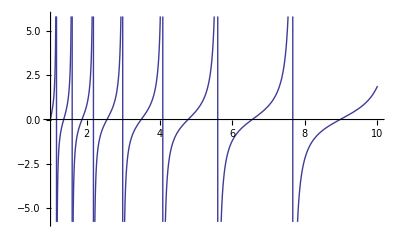

```mathematica
Plot[Re[Tan[t Log[n]+ArcCot[2t]]]/.t->10,{n,1,10}]
```

```mathematica
ArcCot[100.]
```

0.00999967

```mathematica
FullSimplify[j^(-1/2)(Cos[t Log[j]]-I Sin[t Log[j]])]
```

j^(-1/2-ⅈ t)

```mathematica
Sum[j^(-1/2-ⅈ t),{j,1,n}]
```

HarmonicNumber[n,1/2+ⅈ t]

```mathematica
ext5[n_,x_]:=(1/2)(HarmonicNumber[n,1/2-I x]+HarmonicNumber[n,1/2+I x])+(Tan[x Log[n]+ArcCot[2 x]]((1/(2 I))(HarmonicNumber[n,(1/2-I x)]-HarmonicNumber[n,(1/2+I x)])))
ext5a[n_,s_]:=1/2 (HarmonicNumber[n,1/2-ⅈ s]+HarmonicNumber[n,1/2+ⅈ s])-1/2 ⅈ (HarmonicNumber[n,1/2-ⅈ s]-HarmonicNumber[n,1/2+ⅈ s]) Tan[ArcCot[2 s]+s Log[n]]
ext5b[n_,s_]:=1/2 HarmonicNumber[n,1/2-ⅈ s] (1-ⅈ Tan[ArcCot[2 s]+s Log[n]])+1/2 HarmonicNumber[n,1/2+ⅈ s] (1+ⅈ Tan[ArcCot[2 s]+s Log[n]])
ext5c[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]])+1/2 HarmonicNumber[n,1/2-s] (1+Tanh[ArcCoth[2 s]-s Log[n]])
ext5cx[n_,s_]:={1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]]),+1/2 HarmonicNumber[n,1/2-s] (1+Tanh[ArcCoth[2 s]-s Log[n]])}
ext5cy[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]])
```

```mathematica
ext5b[100000000000000,.2I+5000]
```

0.545084+0.2518 ⅈ

```mathematica
ext5c[100000000000,N@ZetaZero@1-1/2]
```

1.58714×10^-6+0. ⅈ

```mathematica
Zeta[N@ZetaZero@1+.1+.3I]
```

0.0711203+0.235516 ⅈ

```mathematica
FullSimplify@ext5[n,s]
```

```mathematica
HarmonicNumber[n,1/2-ⅈ s] (1-ⅈ Tan[ArcCot[2 s]+s Log[n]])/2+HarmonicNumber[n,1/2+ⅈ s] (1+ⅈ Tan[ArcCot[2 s]+s Log[n]])/2
```

1/2 HarmonicNumber[n,1/2-ⅈ s] (1-ⅈ Tan[ArcCot[2 s]+s Log[n]])+1/2 HarmonicNumber[n,1/2+ⅈ s] (1+ⅈ Tan[ArcCot[2 s]+s Log[n]])

```mathematica
Zeta[.7+5000I]
```

0.545082-0.251794 ⅈ

```mathematica
1/2 HarmonicNumber[n,1/2-ⅈ (s/I)] (1-ⅈ Tan[ArcCot[2 (s/I)]+(s/I) Log[n]])+1/2 HarmonicNumber[n,1/2+ⅈ (s/I)] (1+ⅈ Tan[ArcCot[2 (s/I)]+(s/I) Log[n]])
```

1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]])+1/2 HarmonicNumber[n,1/2-s] (1+Tanh[ArcCoth[2 s]-s Log[n]])

```mathematica
ext5cy[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]])
ext5cyc[n_,s_]:=1/2 HarmonicNumber[n,s] (1-Tanh[ArcCoth[2 s-1]-(s-1/2) Log[n]])
ext5cy2[n_,s_]:={1/2 HarmonicNumber[n,1/2+s], (1-Tanh[ArcCoth[2 s]-s Log[n]])}
ext5cy3[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]])+1/2 HarmonicNumber[n,1/2-s] (1+Tanh[ArcCoth[2 s]-s Log[n]])
```

```mathematica
ext5cyc[1000000000000,N@ZetaZero@1]
```

4.91847×10^-7+69217.7 ⅈ

```mathematica
sb[n_,s_]:=n^(s-1/2)(1-s) HarmonicNumber[n,s]
sb2[n_,s_]:=n^(s-1/2)((1-s)/s)^(1/2) HarmonicNumber[n,s]
sb3[n_,s_]:=n^s ((1/2-s)/(1/2+s))^(1/2) HarmonicNumber[n,1/2+s]
```

```mathematica
sb3[10000000000,N@ZetaZero@3-1/2]
```

3997.46-4.9992×10^-6 ⅈ

```mathematica
sb[n,s+1/2]
```

n^s (1/2-s) HarmonicNumber[n,1/2+s]

```mathematica
ext5cyc[n_,s_]:=1/2 HarmonicNumber[n,s] (1-Tanh[ArcCoth[2 s-1]-(s-1/2) Log[n]])
ext5cyc2[n_,s_]:=1/2 HarmonicNumber[n,s+1/2] (1-Tanh[ArcCoth[2 s]-s  Log[n]])
```

```mathematica
ext5cyc5[1000000000000,N@ZetaZero@1-.5]
```

4.91858×10^-7+69217.7 ⅈ

```mathematica
ext5cyc[1000000000000,N@ZetaZero@1]
```

4.91847×10^-7+69217.7 ⅈ

```mathematica
Tanh[ArcCoth[2 s-1]]
```

-1/(1-2 s)

```mathematica
ext3[n_,x_]:=Sum[(((1/2)(j^(-1/2+I x )+ j^(-1/2-I x )))+Tan[x Log[n]+ArcCot[2 x]]((1/(2 I))(j^(-1/2+I x)-j^(-1/2-I x)))),{j,1,n}]
```

```mathematica
ext3[100000,.2I+10]
```

1.47421+0.114901 ⅈ

```mathematica
Zeta[.7+10I]
```

1.47708-0.114696 ⅈ

```mathematica
ext5c[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]])+1/2 HarmonicNumber[n,1/2-s] (1+Tanh[ArcCoth[2 s]-s Log[n]])
ext5d[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] (1-((E^(ArcCoth[2 s]-s Log[n])-E^(-(ArcCoth[2 s]-s Log[n])))/(E^(ArcCoth[2 s]-s Log[n])+E^(-(ArcCoth[2 s]-s Log[n])))))+1/2 HarmonicNumber[n,1/2-s] (1+((E^(ArcCoth[2 s]-s Log[n])-E^(-(ArcCoth[2 s]-s Log[n])))/(E^(ArcCoth[2 s]-s Log[n])+E^(-(ArcCoth[2 s]-s Log[n])))))
ext5e[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] (1-((E^ArcCoth[2 s]E^(-s Log[n])-E^(s Log[n])E^(-ArcCoth[2 s]))/(E^(ArcCoth[2 s])E^(-s Log[n])+E^(s Log[n])E^(-ArcCoth[2 s]))))+1/2 HarmonicNumber[n,1/2-s] (1+((E^ArcCoth[2 s]E^(-s Log[n])-E^(s Log[n])E^(-ArcCoth[2 s]))/(E^(ArcCoth[2 s])E^(-s Log[n])+E^(s Log[n])E^(-ArcCoth[2 s]))))
ext5f[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] ((2 n^(2 s))/(ⅇ^(2 ArcCoth[2 s])+n^(2 s)))+1/2 HarmonicNumber[n,1/2-s] (2/(1+ⅇ^(-2 ArcCoth[2 s]) n^(2 s)))
ext5g[n_,s_]:=1/2 HarmonicNumber[n,1/2+s] ((2 n^(2 s))/((1+2 s)/(-1+2 s)+n^(2 s)))+1/2 HarmonicNumber[n,1/2-s] (2/(1+(-1+2 s)/(1+2 s) n^(2 s)))
ext5h[n_,s_]:= HarmonicNumber[n,1/2+s] (n^(2 s)/((2 s+1)/(2 s-1)+n^(2 s)))+ HarmonicNumber[n,1/2-s] (1/(1+(2 s-1)/(2 s+1) n^(2 s)))
ext5i[n_,s_]:= HarmonicNumber[n,1/2+s] (1/(1+(2 s+1)/(2 s-1)n^(-2 s)))+ HarmonicNumber[n,1/2-s] (1/(1+(2 s-1)/(2 s+1) n^(2 s)))
ext5j[n_,s_]:= HarmonicNumber[n,1/2+s] (1/(1-(1/2+ s)/(1/2- s)n^(-2 s)))+ HarmonicNumber[n,1/2-s] (1/(1-(1/2- s)/(1/2+ s) n^(2 s)))
```

```mathematica
ext5j[100000000,N@ZetaZero@1-.5]
```

-0.0000531084+0. ⅈ

```mathematica
Zeta[.7+10I]
```

1.47708-0.114696 ⅈ

```mathematica
Expand[E^(ArcCoth[2 s])]
```

ⅇ^ArcCoth[2 s]

```mathematica
E^(-2 ArcCoth[ 2s])/.s->1.2+I
```

0.562982+0.257069 ⅈ

```mathematica
E^(-Log[(2s+1)/(2s-1)])/.s->1.2+I
```

0.562982+0.257069 ⅈ

```mathematica
(-1+2 s)/(1+2 s)/.s->1.2+I
```

0.562982+0.257069 ⅈ

```mathematica
E^(2 ArcCoth[ 2s])/.s->1.2+I
```

1.4698-0.671141 ⅈ

```mathematica
E^(Log[(2s+1)/(2s-1)])/.s->1.2+I
```

1.4698-0.671141 ⅈ

```mathematica
(1+2 s)/(-1+2 s)/.s->1.2+I
```

1.4698-0.671141 ⅈ

```mathematica
Integrate[ Cos[2x]Cos[x],{x,-Pi,Pi}]
```

0

```mathematica
FullSimplify[ (1-((E^ArcCoth[2 s]E^(-s Log[n])-E^(s Log[n])E^(-ArcCoth[2 s]))/(E^(ArcCoth[2 s])E^(-s Log[n])+E^(s Log[n])E^(-ArcCoth[2 s]))))]
```

(2 n^(2 s))/(ⅇ^(2 ArcCoth[2 s])+n^(2 s))

```mathematica
FullSimplify[(1+((E^ArcCoth[2 s]E^(-s Log[n])-E^(s Log[n])E^(-ArcCoth[2 s]))/(E^(ArcCoth[2 s])E^(-s Log[n])+E^(s Log[n])E^(-ArcCoth[2 s]))))]
```

2/(1+ⅇ^(-2 ArcCoth[2 s]) n^(2 s))

```mathematica
ⅇ^(-2 ArcCoth[2 s])/.s->1.3
```

0.444444

```mathematica
(-1+2 s)/(1+2 s)/.s->1.3
```

0.444444

```mathematica
E^(-Log[(2s+1)/(2s-1)])
```

(-1+2 s)/(1+2 s)

```mathematica
FullSimplify[(2 s+1)/(2 s-1)]
```

1+2/(-1+2 s)

```mathematica
FullSimplify[HarmonicNumber[n,1/2+s] (1/(1+(2 s+1)/(2 s-1)n^(-2 s)))+ HarmonicNumber[n,1/2-s] (1/(1+(2 s-1)/(2 s+1) n^(2 s)))/.s->s-1/2]
```

(n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s])/(n^(2 s) (-1+s)+n s)

```mathematica
1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]])/.n->100000000/.s->N@ZetaZero@1-1/2
```

-0.0000265542-375.73 ⅈ

```mathematica
HarmonicNumber[n,1/2+s] (1/(1+(2 s+1)/(2 s-1)n^(-2 s)))/.n->100000000/.s->N@ZetaZero@1-1/2
```

-0.0000265542-375.73 ⅈ

```mathematica
HarmonicNumber[n,1/2+s] (1/(1+(2 s+1)/(2 s-1)n^(-2 s)))/.n->100000000/.s->N@ZetaZero@1-1/2
```

```mathematica
HarmonicNumber[n,1/2+s] (1-(1/2+ s)/(1/2- s)n^(-2 s))^-1/.n->100000000/.s->N@ZetaZero@1-1/2
```

-0.0000265542-375.73 ⅈ

```mathematica
FullSimplify[HarmonicNumber[n,1/2+s] (1/(1-(1/2+ s)/(1/2- s)n^(-2 s)))+ HarmonicNumber[n,1/2-s] (1/(1-(1/2- s)/(1/2+ s) n^(2 s)))/.s->s-1/2]
```

(n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s])/(n^(2 s) (-1+s)+n s)

```mathematica
o2[n_,s_]:=n^s((1/2-s)/(1/2+s))^(1/2)HarmonicNumber[n,1/2+s]
o3[n_,s_]:=n^s((1/2-s)/(1/2+s))^(1/2)HarmonicNumber[n,1/2+s]
```

```mathematica
o3[10000000,N@ZetaZero@1-1/2]
```

223.584-0.000158015 ⅈ

```mathematica
HarmonicNumber[n,1/2+s](1-(1/2+ s)/(1/2- s)n^(-2 s))^-1/.n->100000000/.s->N@ZetaZero@1-1/2
```

-0.0000265542-375.73 ⅈ

```mathematica
1/2 HarmonicNumber[n,1/2+s] (1-Tanh[ArcCoth[2 s]-s Log[n]])+1/2 HarmonicNumber[n,1/2-s] (1+Tanh[ArcCoth[2 s]-s Log[n]])/.s->s-1/2
```

1/2 HarmonicNumber[n,s] (1-Tanh[ArcCoth[2 (-1/2+s)]-(-1/2+s) Log[n]])+1/2 HarmonicNumber[n,1-s] (1+Tanh[ArcCoth[2 (-1/2+s)]-(-1/2+s) Log[n]])

```mathematica
bb[n_,s_]:=1/2 HarmonicNumber[n,s] (1-Tanh[ArcCoth[2 (-1/2+s)]-(-1/2+s) Log[n]])+1/2 HarmonicNumber[n,1-s] (1+Tanh[ArcCoth[2 (-1/2+s)]-(-1/2+s) Log[n]])
bb2[n_,s_]:= HarmonicNumber[n,s] (1/2-Tanh[ArcCoth[2s-1]+(1/2-s) Log[n]]/2)+ HarmonicNumber[n,1-s] (1/2+Tanh[ArcCoth[2s-1]+(1/2-s) Log[n]]/2)
bb3[n_,s_]:=1/2 HarmonicNumber[n,1-s]+1/2 HarmonicNumber[n,s]-1/2 HarmonicNumber[n,1-s] Tanh[ArcCoth[1-2 s]-(1/2-s) Log[n]]+1/2 HarmonicNumber[n,s] Tanh[ArcCoth[1-2 s]-(1/2-s) Log[n]]
```

```mathematica
bb3[1000,2.]
```

1.64494

```mathematica
Zeta[.7+31I]
```

0.539212+0.181647 ⅈ

```mathematica
FullSimplify[(1-Tanh[ArcCoth[2 (-1/2+s)]-(-1/2+s) Log[n]])/2]
```

1/2 (1+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])

```mathematica
Expand[HarmonicNumber[n,s] (1/2-Tanh[ArcCoth[2s-1]+(1/2-s) Log[n]]/2)+ HarmonicNumber[n,1-s] (1/2+Tanh[ArcCoth[2s-1]+(1/2-s) Log[n]]/2)]
```

1/2 HarmonicNumber[n,1-s]+1/2 HarmonicNumber[n,s]-1/2 HarmonicNumber[n,1-s] Tanh[ArcCoth[1-2 s]-(1/2-s) Log[n]]+1/2 HarmonicNumber[n,s] Tanh[ArcCoth[1-2 s]-(1/2-s) Log[n]]

```mathematica
HarmonicNumber[n,1/2+s] (1-(1/2+ s)/(1/2- s)n^(-2 s))^-1/.n->100000000/.s->N@ZetaZero@1-1/2
```

-0.0000265542-375.73 ⅈ

```mathematica
HarmonicNumber[n,1/2+s] ((1/2+ s)/(1/2- s))^(-1/2)/(((1/2+ s)/(1/2- s))^(-1/2)-((1/2+ s)/(1/2- s))^(1/2)n^(-2 s))/.n->100000000/.s->N@ZetaZero@1-1/2
```

-0.0000265542-375.73 ⅈ

```mathematica
HarmonicNumber[n,1/2+s] ((1/2+ s)/(1/2- s))^(-1/2)n^s/(((1/2+ s)/(1/2- s))^(-1/2)n^s-((1/2+ s)/(1/2- s))^(1/2)n^(- s))/.n->100000000000/.s->N@ZetaZero@1-1/2
```

7.93571×10^-7+11230.6 ⅈ

```mathematica
HarmonicNumber[n,1/2+s] ((1/2- s)/(1/2+ s))^(1/2)n^s/(((1/2- s)/(1/2+ s))^(1/2)n^s-((1/2- s)/(1/2+ s))^(-1/2)n^(- s))/.n->100000000000/.s->N@ZetaZero@1-1/2
```

7.93571×10^-7+11230.6 ⅈ

```mathematica
HarmonicNumber[n,1/2+s] ((1/2- s)/(1/2+ s))^(1/2)n^s/.n->100000000000/.s->N@ZetaZero@1-1/2
```

22358.4-1.57988×10^-6 ⅈ

```mathematica
HarmonicNumber[n,1/2+s] (1/2- s)n^s/.n->10000000000000000/.s->N@ZetaZero@1-1/2
```

1.×10^8+2.08616×10^-7 ⅈ

```mathematica
HarmonicNumber[n,1/2+s] (1/2-s)n^s/((1/2-s)n^s-(1/2+s)n^(- s))/.n->100000000000000/.s->N@ZetaZero@1-1/2
```

-4.61587×10^-8-357759. ⅈ

```mathematica
HarmonicNumber[n,1/2+s] (1/2-s)n^s/((1/2-s)n^s-(1/2+s)n^(- s))/.s->s-1/2
```

(n^(-1/2+s) (1-s) HarmonicNumber[n,s])/(n^(-1/2+s) (1-s)-n^(1/2-s) s)

```mathematica
HarmonicNumber[n,1/2+s] (1-(1/2+ s)/(1/2- s)n^(-2 s))^-1/.s->s-1/2
```

HarmonicNumber[n,s]/(1-(n^(-2 (-1/2+s)) s)/(1-s))

```mathematica
FullSimplify[1/(1-(n^(-2 (-1/2+s)) s)/(1-s))]
```

1/(1+(n^(1-2 s) s)/(-1+s))

```mathematica
cc[n_,s_]:= Sum[ 1/2 (1+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]) j^-s,{j,1,n}]
cd[n_,s_]:= Sum[ (1+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]) j^-s+ (1-Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]) j^(s-1),{j,1,n}]
cd2[n_,s_]:= (1/2)Sum[j^-s+j^(s-1) +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]] j^-s -Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]] j^(s-1),{j,1,n}]
cd3[n_,s_]:= (1/2)Sum[j^-s+j^(s-1) +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s-j^(s-1)),{j,1,n}]
cd4[n_,s_]:= (1/2)Sum[j^-s+j^(s-1) +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s-j^(s-1)),{j,1,n}]
cd4a[n_,s_]:= DiscretePlot[Re[j^-s+j^(s-1) +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s-j^(s-1))],{j,1,n}]
```

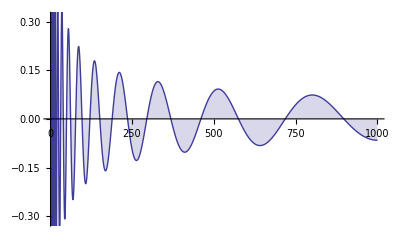

```mathematica
cd4a[1000,N@ZetaZero@1]
```

```mathematica
FullSimplify[(1/2)Sum[j^-s+j^(s-1) +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s-j^(s-1)),{j,1,n}]]
```

1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]+(-HarmonicNumber[n,1-s]+HarmonicNumber[n,s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])

```mathematica
pd[n_,s_]:= (1/2)Sum[j^-s+j^(s-1) +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s-j^(s-1)),{j,1,n}]
pdp[n_,s_]:= (1/2)Sum[j^-s-j^(s-1) +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s+j^(s-1)),{j,1,n}]
pd0[n_,s_,j_]:= j^-s+j^(s-1) +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s-j^(s-1))
pda[n_,s_,j_]:={j^-s,+j^(s-1) ,+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s),Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( -j^(s-1))}
pdb[n_,s_,j_]:= {j^-s+j^(s-1) ,+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s-j^(s-1))}
pdc[n_,s_,j_]:={ j^-s +Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]( j^-s) ,+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( -j^(s-1))+j^(s-1)}
pdc2[n_,s_]:= (1/2)Sum[j^-s+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s),{j,1,n}]
pdc3[n_,s_]:= (1/2)(1+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])HarmonicNumber[n,s]
pdd[n_,s_,j_]:={ j^-s +Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( -j^(s-1)),+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]( j^-s)+j^(s-1)}
pdt[n_,s_,t_]:=(1/2)Sum[j^-(s+t I)+j^((s+t I)-1) +Tanh[ArcCoth[1-2 (s+t I)]-Log[n]/2+(s+t I) Log[n]]( j^-(s+t I)-j^((s+t I)-1)),{j,1,n}]
pdt2[n_,s_,t_]:=(1/2)Sum[j^-(s+t I)+j^((s+t I)-1) +Tanh[ArcCoth[1-2 (s+t I)]-Log[n]/2+(s+t I) Log[n]]( j^-(s+t I)-j^((s+t I)-1)),{j,1,n}]
```

```mathematica
pdc3[10000000000000,.4+10I]
```

12631.-9571.55 ⅈ

```mathematica
pdc[100000,N@ZetaZero@1,2]
```

{-0.484159+0.703598 ⅈ,-0.484159-0.703598 ⅈ}

```mathematica
FullSimplify[j^(1/2+b I)+j^(1-(1/2+b I)) - c(j^(1/2+b I)-j^(1-(1/2+b I)))]
```

j^(1/2-ⅈ b) (1+c-(-1+c) j^(2 ⅈ b))

```mathematica
FullSimplify[j^(a+b I)+j^(1-(a+b I)) - c(j^(a+b I)-j^(1-(a+b I)))]
```

(1+c) j^(1-a-ⅈ b)-(-1+c) j^(a+ⅈ b)

```mathematica
pdt3[100000,0,N@Im@ZetaZero@1]
```

0.542101-0.0498584 ⅈ

```mathematica
j^-(s+t I)+j^((s+t I)-1) +Tanh[ArcCoth[1-2 (s+t I)]-Log[n]/2+(s+t I) Log[n]]( j^-(s+t I)-j^((s+t I)-1))
```

j^(-s-ⅈ t)+j^(-1+s+ⅈ t)+(j^(-s-ⅈ t)-j^(-1+s+ⅈ t)) Tanh[ArcCoth[1-2 (s+ⅈ t)]-Log[n]/2+(s+ⅈ t) Log[n]]

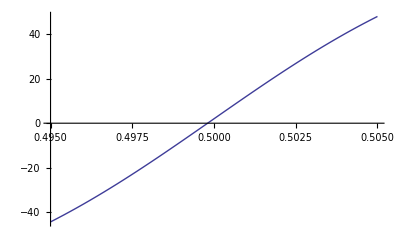

```mathematica
Plot[Re[pdc3[1000000,s+N@ZetaZero@1-.5+1I]],{s,.495,.505}]
```

```mathematica
Re[pdc3[10000000000000,.5+N@ZetaZero@1-.5+1I]]
```

-0.216907

```mathematica
(1-Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])/2/.s->N@ZetaZero@1+.1/.n->1000000000000000000
```

-0.000250713-0.0000182582 ⅈ

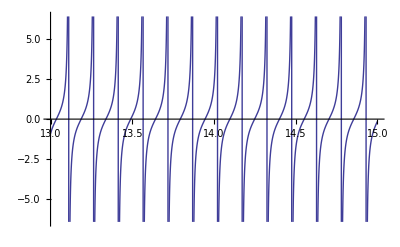

```mathematica
Plot[ Im[ Tanh[ArcCoth[1-2 (1/2+s I)]-Log[n]/2+(1/2+s I) Log[n]]]/.n->1000000000,{s,13,15}]
```

```mathematica
(1/2)(1+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])/.s->N@ZetaZero@10+.1/.n->10000000
```

1.02716+0.030594 ⅈ

```mathematica
(1/2)(1+Tanh[ArcCoth[-2 s]+s Log[n]])/.s->N@ZetaZero@10-.5+.1/.n->1000000000
```

1.0077+0.0139921 ⅈ

```mathematica
pdc3x[n_,s_]:= {(1+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])/2,HarmonicNumber[n,s],(1+Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])/2HarmonicNumber[n,s]}
```

```mathematica
pdc3x[100000000,N@ZetaZero@1+.1]
```

{0.980761-0.0154127 ⅈ,38.786-105.174 ⅈ,36.4188-103.749 ⅈ}

```mathematica
(0.5-1.3930927462873348 ⅈ)(-6654.70681368401+2388.4651062216653 ⅈ)
```

7.39581×10^-6+10464.9 ⅈ

```mathematica
dx[n2_,s_]:=Plot[{ Re[ HarmonicNumber[ n,s]],Im[ HarmonicNumber[ n,s]], Im[(1+Tanh[ArcCoth[1-2s]-Log[n]/2+N@s Log[n]])/2]},{n,1,n2}]
```

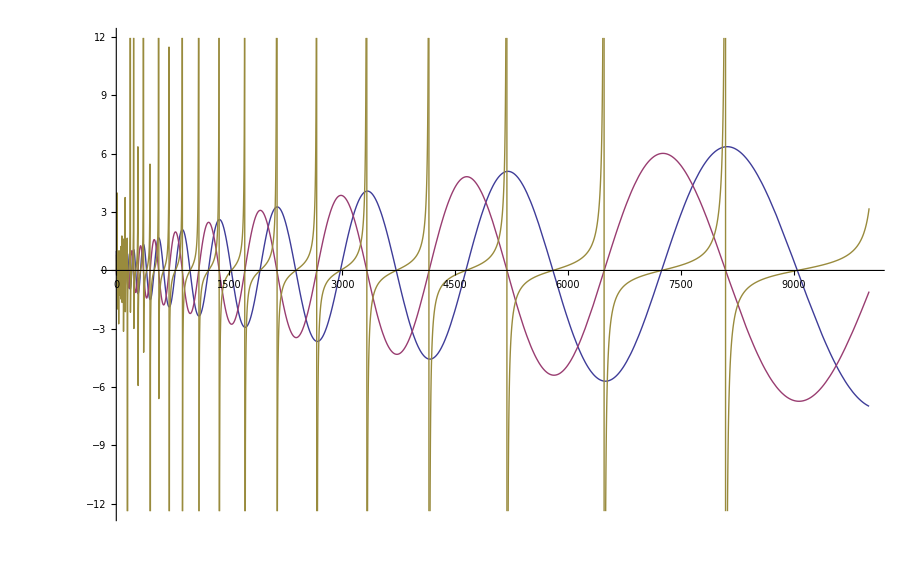

```mathematica
dx[10000,N@ZetaZero@1]
```

```mathematica
pdc3e[100000,1/2,N@Im@ZetaZero@1]
```

-6.26931+4.24706 ⅈ

```mathematica
Tanh[-x]
```

-Tanh[x]

```mathematica
ook[n_,s_]:=1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]+(-HarmonicNumber[n,1-s]+HarmonicNumber[n,s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])
ook2[n_,s_]:={1/2 (HarmonicNumber[n,s](1+ Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])),1/2 (HarmonicNumber[n,1-s](1- Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]))}
ook2x[n_,s_]:={ {HarmonicNumber[n,s],(1+ Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])},{HarmonicNumber[n,1-s],(1- Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])}}
ook2a[n_,s_]:=Re[1/2 (HarmonicNumber[n,s](1+ Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]))]+Re[1/2 (HarmonicNumber[n,1-s](1- Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]))]
ook3[n_,s_]:={1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]),(1/2)((HarmonicNumber[n,s]-HarmonicNumber[n,1-s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])}
ook3a[n_,s_]:=1/2 (HarmonicNumber[n,s]+(HarmonicNumber[n,s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])
ook3b[n_,s_]:=(1/2)(HarmonicNumber[n,1-s]-(HarmonicNumber[n,1-s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])
ook4[n_,s_]:={1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]),(1/2)((HarmonicNumber[n,s]-HarmonicNumber[n,1-s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])}
ook4o[n_,s_]:={ {HarmonicNumber[n,s],HarmonicNumber[n,1-s]},{HarmonicNumber[n,s],-HarmonicNumber[n,1-s],Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]}}
ook4a[n_,s_]:=1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s])
ook4b[n_,s_]:=(1/2)((HarmonicNumber[n,s]-HarmonicNumber[n,1-s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])
```

```mathematica
ook[1000000000000000000000,N@ZetaZero@1+.1]
```

0.0753326+0.011364 ⅈ

```mathematica
Zeta[10I+.6]
```

1.50992-0.115339 ⅈ

```mathematica
ook3[10000000000,10I+.6]
```

{-41919.+27425.3 ⅈ,41920.5-27425.5 ⅈ}

```mathematica
ook4o[1000000,.9+20I]
```

{{0.629021-0.538723 ⅈ,-1314.46-12476.1 ⅈ},{0.629021-0.538723 ⅈ,1314.46+12476.1 ⅈ,0.999969-7.84716×10^-6 ⅈ}}

```mathematica
(0.6290209794817144-0.5387228886380006 ⅈ)+(-1314.456626857418-12476.12256231477 ⅈ)
```

-1313.83-12476.7 ⅈ

```mathematica
-((0.6290209794817144-0.5387228886380006 ⅈ)+(1314.456626857418+12476.12256231477 ⅈ))(0.9999692566250131-7.847163490931001*^-6 ⅈ)
```

-1315.14-12475.2 ⅈ

```mathematica
-((0.6290209794817144-0.5387228886380006 ⅈ)+(1314.456626857418+12476.12256231477 ⅈ))
```

-1315.09-12475.6 ⅈ

```mathematica
ook4o[1000000,N@ZetaZero@10+.3]
```

{{0.407264-0.179835 ⅈ,424.325+1194.49 ⅈ},{0.407264-0.179835 ⅈ,-424.325-1194.49 ⅈ,0.999614-0.000321891 ⅈ}}

```mathematica
ook2[100000000000,N@ZetaZero@10+.1]
```

{-401.038-307.544 ⅈ,401.154+307.601 ⅈ}

```mathematica
FullSimplify[j^-s-j^(s-1)]
```

-j^(-1+s)+j^-s

```mathematica
tt[n_,s_]:=(1+ Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]])/2
tt2[n_,s_]:=(1- Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]])/2
tt3[n_,s_]:=(1(1+ Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]])+(2^s Pi^(s-1)Sin[Pi s / 2]Gamma[1-s])(1-Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]))/2
tt4[n_,s_]:=(1(1+ Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]])+(2^(1-s) π^-s Gamma[s] Sin[1/2 π (1-s)])(1-Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]))/2
```

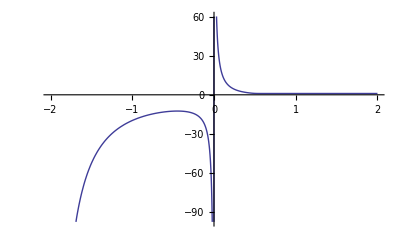

```mathematica
Plot[ tt4[10000000000000000,t],{t,-2,2}]
```

```mathematica
(2^s Pi^(s-1)Sin[Pi s / 2]Gamma[1-s])Zeta[1-s]/.s->2.0000000001
```

1.64493

```mathematica
tt4[10000000000,1-s]Zeta[1-s]/.s->2.0000000001
```

1.64493

```mathematica
(2^s Pi^(s-1)Sin[Pi s / 2]Gamma[1-s])/.s->1-s
```

2^(1-s) π^-s Gamma[s] Sin[1/2 π (1-s)]

```mathematica
FullSimplify[(1(1+ Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]])+f[s](1-Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]))/2]
```

1/2 (1+f[s]-(-1+f[s]) Tanh[ArcCoth[1-2 s]+(-1/2+s) Log[n]])

```mathematica
FullSimplify[(1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]+(-HarmonicNumber[n,1-s]+HarmonicNumber[n,s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]))((1(1+ Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]])+f[s](1-Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]))/2)]
```

((n^(2 s) (-1+s)+n s f[s]) (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((n^(2 s) (-1+s)+n s)^2)

```mathematica
ff[s_]:=(2^s Pi^(s-1)Sin[Pi s / 2]Gamma[1-s])
ach[n_,s_]:=((n^(2 s) (-1+s)+n s ff[s]) (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((n^(2 s) (-1+s)+n s)^2)
ach2[n_,s_]:=((n^s (-1+s)+n^(1-s) s ff[s]) (n^(1-s) s HarmonicNumber[n,1-s]+n^s (-1+s) HarmonicNumber[n,s]))/((n^s (-1+s)+n^(1-s) s)^2)
ach3[n_,s_]:=((n^s (-1+s)+n^(1-s) s ff[s]) (n^(1-s) s HarmonicNumber[n,1-s]))/((n^s (-1+s)+n^(1-s) s)^2)+((n^s (-1+s)+n^(1-s) s ff[s]) (n^s (-1+s) HarmonicNumber[n,s]))/((n^s (-1+s)+n^(1-s) s)^2)
```

```mathematica
ach3[10000000000,.3]
```

-0.904264

```mathematica
Zeta[.3]
```

-0.904559

```mathematica
Expand[((n^(2 s) (-1+s)+n s ff[s]) (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((n^(2 s) (-1+s)+n s)^2)]
```

-(n^(1+2 s) s HarmonicNumber[n,1-s])/((n^(2 s) (-1+s)+n s)^2)+(n^(1+2 s) s^2 HarmonicNumber[n,1-s])/((n^(2 s) (-1+s)+n s)^2)+(n^(4 s) HarmonicNumber[n,s])/((n^(2 s) (-1+s)+n s)^2)-(2 n^(4 s) s HarmonicNumber[n,s])/((n^(2 s) (-1+s)+n s)^2)+(n^(4 s) s^2 HarmonicNumber[n,s])/((n^(2 s) (-1+s)+n s)^2)+(2^s n^2 π^(-1+s) s^2 Gamma[1-s] HarmonicNumber[n,1-s] Sin[(π s)/2])/((n^(2 s) (-1+s)+n s)^2)-(2^s n^(1+2 s) π^(-1+s) s Gamma[1-s] HarmonicNumber[n,s] Sin[(π s)/2])/((n^(2 s) (-1+s)+n s)^2)+(2^s n^(1+2 s) π^(-1+s) s^2 Gamma[1-s] HarmonicNumber[n,s] Sin[(π s)/2])/((n^(2 s) (-1+s)+n s)^2)

```mathematica
acha[n_,s_]:=(n^(4 s) HarmonicNumber[n,s])/((n^(2 s) (-1+s)+n s)^2)-(2 n^(4 s) s HarmonicNumber[n,s])/((n^(2 s) (-1+s)+n s)^2)+(n^(4 s) s^2 HarmonicNumber[n,s])/((n^(2 s) (-1+s)+n s)^2)-(2^s n^(1+2 s) π^(-1+s) s Gamma[1-s] HarmonicNumber[n,s] Sin[(π s)/2])/((n^(2 s) (-1+s)+n s)^2)
achb[n_,s_]:=-(n^(1+2 s) s HarmonicNumber[n,1-s])/((n^(2 s) (-1+s)+n s)^2)+(n^(1+2 s) s^2 HarmonicNumber[n,1-s])/((n^(2 s) (-1+s)+n s)^2)+(2^s n^2 π^(-1+s) s^2 Gamma[1-s] HarmonicNumber[n,1-s] Sin[(π s)/2])/((n^(2 s) (-1+s)+n s)^2)+(2^s n^(1+2 s) π^(-1+s) s^2 Gamma[1-s] HarmonicNumber[n,s] Sin[(π s)/2])/((n^(2 s) (-1+s)+n s)^2)
```

```mathematica
FullSimplify[acha[n,s]]
```

(n^(2 s) HarmonicNumber[n,s] (n^(2 s) π (-1+s)^2-n (2 π)^s s Gamma[1-s] Sin[(π s)/2]))/(π (n^(2 s) (-1+s)+n s)^2)

```mathematica
(1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]+(-HarmonicNumber[n,1-s]+HarmonicNumber[n,s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]))((1(1+ Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]])+(2^s Pi^(s-1)Sin[Pi s / 2]Gamma[1-s])(1-Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]))/2)/.n->1000000000000/.s->N@ZetaZero@1
```

-2.32786×10^-7+1.46223×10^-6 ⅈ

```mathematica
ook2s[n_,s_]:=1/2 (HarmonicNumber[n,s](1+ Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])+(ff[1-s]HarmonicNumber[n,1-s])(1- Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]))
ook2t[n_,s_]:=(1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]+(-HarmonicNumber[n,1-s]+HarmonicNumber[n,s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]))((1+ Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]+(2^s Pi^(s-1)Sin[Pi s / 2]Gamma[1-s])(1-Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]))/2)
```

```mathematica
ach3[n_,s_]:=((n^s (-1+s)+n^(1-s) s ff[s]) (n^(1-s) s HarmonicNumber[n,1-s]))/((n^s (-1+s)+n^(1-s) s)^2)+((n^s (-1+s)+n^(1-s) s ff[s]) (n^s (-1+s) HarmonicNumber[n,s]))/((n^s (-1+s)+n^(1-s) s)^2)
ach4[n_,s_]:=(n^(2s-1) (-1+s)/s+ ff[s])/((n^(2s-1) (-1+s)/s+ 1)^2)HarmonicNumber[n,1-s]+((n^s (-1+s)+n^(1-s) s ff[s]) (n^s (-1+s) HarmonicNumber[n,s]))/((n^s (-1+s)+n^(1-s) s)^2)
ach5[n_,s_]:=(n^(2s-1) (-1+s)/s+ ff[s])/((n^(2s-1) (-1+s)/s+ 1)^2)HarmonicNumber[n,1-s]+(1+n^(1-2s) s/(s-1) ff[s])/((1+n^(1-2s) s/(s-1))^2)HarmonicNumber[n,s]
ach6[n_,s_]:=(n^(2s-1) (-1+s)/s+ ff[s])/((n^(2s-1) (-1+s)/s+ 1)^2)HarmonicNumber[n,1-s]+(1+n^(1-2s) s/(s-1) ff[s])/((1+n^(1-2s) s/(s-1))^2)HarmonicNumber[n,s]
```

```mathematica
ach6[1000000000,.3+3I]
```

0.494697-0.063197 ⅈ

```mathematica
Zeta[.3+3I]
```

0.49469-0.0632084 ⅈ

```mathematica
FullSimplify[(n^(2s-1) (-1+s)/s+ ff[s])/((n^(2s-1) (-1+s)/s+ 1)^2)HarmonicNumber[n,1-s]+(1+n^(1-2s) s/(s-1) ff[s])/((1+n^(1-2s) s/(s-1))^2)HarmonicNumber[n,s]]
```

((n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]) (n^(2 s) π (-1+s)+n (2 π)^s s Gamma[1-s] Sin[(π s)/2]))/(π (n^(2 s) (-1+s)+n s)^2)

```mathematica
ook2t[n_,s_]:=(1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]+(-HarmonicNumber[n,1-s]+HarmonicNumber[n,s]) Tanh[ArcCoth[1-2 s]-Log[n]/2+s Log[n]]))((1+ Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]+(2^s Pi^(s-1)Sin[Pi s / 2]Gamma[1-s])(1-Tanh[ArcCoth[1-2 s]+(s-1/2) Log[n]]))/2)
ook2tr[n_,s_]:=(1/2 (HarmonicNumber[n,1-s]+HarmonicNumber[n,s]+(-HarmonicNumber[n,1-s]+HarmonicNumber[n,s]) Tanh[-Log[n]/2+s Log[n]]))((1+ Tanh[(s-1/2) Log[n]]+(2^s Pi^(s-1)Sin[Pi s / 2]Gamma[1-s])(1-Tanh[(s-1/2) Log[n]]))/2)
```

```mathematica
ook2t[10000000,.2+10I]
```

1.66396-0.110343 ⅈ

```mathematica
Zeta[.2+10I]
```

1.66396-0.110342 ⅈ

```mathematica
x Sin[x Log[n]]+1/2 Cos[x Log[n]]/.x->.3+2I/.n->20
```

-139.83+272.118 ⅈ

```mathematica
Cos[x Log[n]](x Tan[x Log[n]]+1/2)/.x->.3+2I/.n->20
```

-139.83+272.118 ⅈ

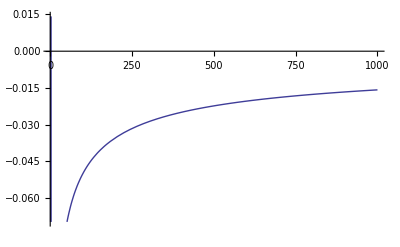

```mathematica
Plot[Im[((1/2-s)/(1/2+s))^(1/2)n^s  HarmonicNumber[n,1/2+s]]/.s->N@ZetaZero@1-.5,{n,1,1000}]
```

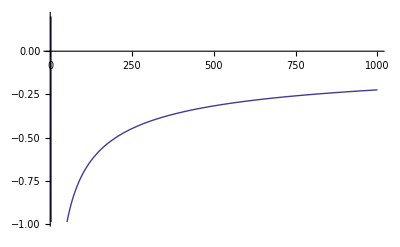

```mathematica
Plot[Im[((1/2-s))n^s  HarmonicNumber[n,1/2+s]]/.s->N@ZetaZero@1-.5,{n,1,1000}]
```

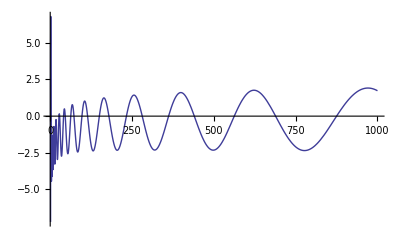

```mathematica
FullSimplify[((1/2+t I)(1/2-t I))^(1/2)]
```

1/2 √(1+4 t^2)

```mathematica
FullSimplify[1/2 √(1+4 t^2)/(1/2+t I)]
```

(1-2 ⅈ t)/(√(1+4 t^2))

```mathematica
FullSimplify[1/2 √(1+4 t^2)/(1/2-t I)]
```

(1+2 ⅈ t)/(√(1+4 t^2))

```mathematica
FullSimplify[((1/2+t I)(1/2-t I))^(1/2)/(1/2+t I)]
```

(1-2 ⅈ t)/(√(1+4 t^2))

```mathematica
ts[n_,t_]:= n^(1/2+t I)/(1/2+t I) +  n^(1/2-t I)/(1/2-t I)
ts2[n_,t_]:=n^(1/2)(2 n^(-ⅈ t)+2 n^(ⅈ t)+4 ⅈ n^(-ⅈ t) t-4 ⅈ n^(ⅈ t) t)/(1+4 t^2)
ts3[n_,t_]:=n^(1/2)(2 (n^(ⅈ t)+ n^(-ⅈ t))+(4 t I)(  n^(-ⅈ t) - n^(ⅈ t) ))/(1+4 t^2)
ts4[n_,t_]:=n^(1/2)(4 Cos[t Log[n]]+(4 t I)(2 I Sin[-t Log[n]]))/(1+4 t^2)
ts5[n_,t_]:=n^(1/2)8(t Sin[t Log[n]]+(1/2) Cos[t Log[n]])/(1+(2t)^2)
ts6[n_,t_]:=n^(1/2)8(t Sin[t Log[n]]+(1/2) Cos[t Log[n]])Cos[ArcTan[2 t]]^2
ts7[n_,t_]:=n^(1/2)(2t Sin[t Log[n]]+ Cos[t Log[n]])/(1/4+t^2)
```

```mathematica
N[ts7[10,14]]
```

0.340949

```mathematica
FullSimplify[ts[n,t]]
```

(2 n^(1/2-ⅈ t) (1+n^(2 ⅈ t) (1-2 ⅈ t)+2 ⅈ t))/(1+4 t^2)

```mathematica
Expand[2 n^(1/2-ⅈ t) (1+n^(2 ⅈ t) (1-2 ⅈ t)+2 ⅈ t)]
```

2 n^(1/2-ⅈ t)+2 n^(1/2+ⅈ t)+4 ⅈ n^(1/2-ⅈ t) t-4 ⅈ n^(1/2+ⅈ t) t

```mathematica
FullSimplify[n^(1/2+t I)/(1/2+t I) +  n^(1/2-t I)/(1/2-t I)]
```

(2 n^(1/2-ⅈ t) (1+n^(2 ⅈ t) (1-2 ⅈ t)+2 ⅈ t))/(1+4 t^2)

```mathematica
(4 t I)(2 I)
```

-8 t

```mathematica
n^(1/2)8Cos[t Log[n]](t Tan[t Log[n]]+(1/2) )/((1+4 t^2))
```

(8 √n Cos[t Log[n]] (1/2+t Tan[t Log[n]]))/(1+4 t^2)

```mathematica
Cos[ArcTan[2t]]
```

1/(√(1+4 t^2))

```mathematica
n^(1/2)8(t Sin[t Log[n]]+(1/2) Cos[t Log[n]])(Cos[ArcTan[2 t]])
```

(8 √n (1/2 Cos[t Log[n]]+t Sin[t Log[n]]))/(√(1+4 t^2))

```mathematica
FullSimplify[n^(1/2)8(t Sin[t Log[n]]+(1/2) Cos[t Log[n]])(Cos[ArcTan[2 t]]Cos[ArcTan[2 t]])]
```

(4 √n (Cos[t Log[n]]+2 t Sin[t Log[n]]))/(1+4 t^2)

```mathematica
FullSimplify[(1/2+t I)(1/2-t I)]
```

1/4+t^2

```mathematica
FullSimplify[n^(1/2)(2t Sin[t Log[n]]+ Cos[t Log[n]])/(1/4+t^2)]
```

(√n (Cos[t Log[n]]+2 t Sin[t Log[n]]))/(1/4+t^2)

```mathematica
(2t Sin[t Log[n]]+ Cos[t Log[n]])/(2t Cos[t Log[n]]- Sin[t Log[n]])/.t->.3/.n->20
```

-2.67049

```mathematica
Sin[t Log[n]+ArcCot[2t]]/Cos[t Log[n]+ArcCot[2t]]/.t->.3/.n->20
```

-2.67049

```mathematica
(Tan[t Log[n]]+1/(2 t))/(1- Tan[t Log[n]]/(2 t))/.t->.3/.n->20
```

-2.67049

```mathematica
(Tan[t Log[n]]+1/(2 t))/(2t Cos[t Log[n]])/.t->.3/.n->20
```

7.82594

```mathematica
FullSimplify[(Tan[t Log[n]]+1/(2 t))(2t Cos[t Log[n]])]
```

Cos[t Log[n]]+2 t Sin[t Log[n]]

```mathematica
FullSimplify[(Tan[x]+a)/(1-a Tan[x])]
```

(a+Tan[x])/(1-a Tan[x])

```mathematica
Tan[ArcTan[1/(2x)]]
```

1/(2 x)

```mathematica
Tan[ArcCot[2x]]
```

1/(2 x)

```mathematica
FullSimplify[(Tan[a]+Tan[b])/(1-Tan[a]Tan[b])]
```

Tan[a+b]

```mathematica
ArcTan[0]
```

0

```mathematica
FullSimplify[(Tan[a])/(1-Tan[a])]
```

1/(-1+Cot[a])

```mathematica
Tanh[ArcCoth[2s]]
```

1/(2 s)

```mathematica
FullSimplify[-1/((I t +1/2)(I t-1/2))]
```

4/(1+4 t^2)

```mathematica
pl[t_]:= 1/(t^2+1/4)
```

```mathematica
pl[N@Im@ZetaZero@1]
```

0.00499899

```mathematica
ts7[n_,t_]:=n^(1/2)(2t Sin[t Log[n]]+ Cos[t Log[n]])/(1/4+t^2)
ts8[n_,t_]:=n^(1/2)(2t Sin[t Log[n]]+ Cos[t Log[n]])/(1/4+t^2)
```

```mathematica
ts7[20,13.3]
```

0.550476

```mathematica
FullSimplify[(1/2-t I)(1/2+t I)]
```

1/4+t^2

```mathematica
os[n_,t_]:= n^(1/2+t I)/((1/2+t I)) +  n^(1/2-t I)/(1/2-t I)
os2[n_,t_]:= ((1/2+t I)/(1/2-t I))^(-1/2)n^(1/2+t I)/(((1/2+t I)/(1/2-t I))^(-1/2)(1/2+t I)) +  ((1/2-t I)/(1/2+t I))^(-1/2)n^(1/2-t I)/(((1/2-t I)/(1/2+t I))^(-1/2)(1/2-t I))
os3[n_,t_]:= ((1/2+t I)/(1/2-t I))^(-1/2)n^(1/2+t I)/
(((1/2+t I)^(1/2)/(1/2-t I)^(-1/2))) + 
 ((1/2-t I)/(1/2+t I))^(-1/2)n^(1/2-t I)/
(((1/2-t I)^(1/2)/(1/2+t I)^(-1/2)))
os4[n_,t_]:= ((1/2+t I)/(1/2-t I))^(-1/2)n^(1/2+t I)/
(((1/2+t I)^(1/2)/(1/2-t I)^(-1/2))) + 
 ((1/2-t I)/(1/2+t I))^(-1/2)n^(1/2-t I)/
(((1/2-t I)^(1/2)/(1/2+t I)^(-1/2)))
os5[n_,t_]:= n^(1/2)(((1/2+t I)/(1/2-t I))^(-1/2)n^(t I)
+ ((1/2-t I)/(1/2+t I))^(-1/2)n^(-t I))/
((1/2-t I)(1/2+t I))^(1/2)
os6[n_,t_]:= n^(1/2)(((1/2-t I)/(1/2+t I))^(1/2)n^(t I)+ ((1/2-t I)/(1/2+t I))^(-1/2)n^(-t I))/((1/2-t I)(1/2+t I))^(1/2)
os7[n_,t_]:= n^(1/2)(E^Log[((1/2-t I)/(1/2+t I))^(1/2)]E^(t I Log[n])+ ((1/2-t I)/(1/2+t I))^(-1/2)n^(-t I))/((1/2-t I)(1/2+t I))^(1/2)
os8[n_,t_]:= n^(1/2)(E^(-I ArcTan[2t])E^(t I Log[n])+ E^(I ArcTan[2t])n^(-t I))/((1/2-t I)(1/2+t I))^(1/2)
os9[n_,t_]:= n^(1/2)(E^(-I ArcTan[2t])E^( I (t Log[n]))+ E^(I ArcTan[2t])E^(- I (t Log[n])))/((1/2-t I)(1/2+t I))^(1/2)
os10[n_,t_]:= n^(1/2)(E^( I (t Log[n]- ArcTan[2t]))+ E^(-I (t Log[n]-ArcTan[2t])))/((1/2-t I)(1/2+t I))^(1/2)
os11[n_,t_]:= n^(1/2)2 Cos[t Log[n]- ArcTan[2t]]/((1/2-t I)(1/2+t I))^(1/2)
os12[n_,t_]:= 4n^(1/2) Cos[t Log[n]- ArcTan[2t]]Cos[ArcTan[2t]]
os13[n_,t_]:= 2n^(1/2) (Cos[t Log[n]]+Cos[t Log[n]-2 ArcTan[2t]])
```

```mathematica
os13[12,13.3]
```

0.517943

```mathematica
((1/2+t I)/(1/2-t I))^(-1/2)
```

1/(√((1/2+ⅈ t)/(1/2-ⅈ t)))

```mathematica
((1/2-t I)/(1/2+t I))^(-1/2)
```

1/(√((1/2-ⅈ t)/(1/2+ⅈ t)))

```mathematica
FullSimplify[(((1/2+t I)/(1/2-t I))^(-1/2)(1/2+t I))]
```

(√(1+2 ⅈ t))/(2 √(1/(1-2 ⅈ t)))

```mathematica
(((1/2-t I)^(1/2)/(1/2+t I)^(-1/2)))
```

√(1/2-ⅈ t) √(1/2+ⅈ t)

```mathematica
(((1/2+t I)^(1/2)/(1/2-t I)^(-1/2)))
```

√(1/2-ⅈ t) √(1/2+ⅈ t)

```mathematica
FullSimplify[Log[((1/2-t I)/(1/2+t I))^(1/2)]]
```

Log[√((ⅈ+2 t)/(ⅈ-2 t))]

```mathematica
Log[√((ⅈ+2 t)/(ⅈ-2 t))]/.t->.7
```

-1.11022×10^-16-0.950547 ⅈ

```mathematica
ArcTan[2(1.3+I)]/I
```

0.177123-1.32603 ⅈ

```mathematica
FullSimplify[ Log[((1/2-t I)/(1/2+t I))^(1/2)]]/.t->(1.3+I)
```

0.177123-1.32603 ⅈ

```mathematica
ArcTanh[-2I(1.3+I)]
```

0.177123-1.32603 ⅈ

```mathematica
ArcTanh[-2I t]
```

-ⅈ ArcTan[2 t]

```mathematica
ArcTan[2 t]/I
```

-ⅈ ArcTan[2 t]

```mathematica
FullSimplify[2/((1/2-t I)(1/2+t I))^(1/2)]
```

4/(√(1+4 t^2))

```mathematica
Cos[t Log[n]- ArcTan[2t]]Cos[ArcTan[2t]]
```

```mathematica
FullSimplify[Cos[t Log[n]-2 ArcTan[2t]]]
```

```mathematica
Cos[2 ArcTan[2 t]]
```

```mathematica
Cos[ ArcTan[2 t]+ ArcTan[2 t]]
```

Cos[2 ArcTan[2 t]]

```mathematica
FullSimplify[ Log[((1/2-t I)/(1/2+t I))^(1/2)]]
```

Log[√((ⅈ+2 t)/(ⅈ-2 t))]

```mathematica
FullSimplify[ Log[((1/2-s)/(1/2+s))^(1/2)]]/.s->(1.3+I)
```

-0.237467-1.37632 ⅈ

```mathematica
ArcTanh[-2(1.3+I)]
```

-0.237467-1.37632 ⅈ

```mathematica
ArcTanh[-2s]
```

-ArcTanh[2 s]

```mathematica
zt[n_,s_]:=Sum[ j^(-1/2) Sinh[s Log[n/j]-ArcTanh[2 s]]/Sinh[s Log[n]-ArcTanh[2 s]],{j,1,n}]
zta[n_,s_]:=Sum[ j^(-1/2) (Cosh[s Log[j]]-(Cosh[s Log[n]-ArcTanh[2 s]]Sinh[s Log[j]])/Sinh[s Log[n]-ArcTanh[2 s]]),{j,1,n}]
ztb[n_,s_]:=Sum[ j^(-1/2) (Cosh[s Log[j]]-(Cosh[s Log[n]-ArcTanh[2 s]]Sinh[s Log[j]])/Sinh[s Log[n]-ArcTanh[2 s]]),{j,1,n}]
zt2[n_,s_]:=Sum[ j^(-1/2) (Cosh[s Log[j]]-Sinh[s Log[j]]Tanh[s Log[n]-ArcTanh[1/(2s)]]),{j,1,n}]
zt2a[n_,s_]:=Sum[ j^(-1/2) (Cos[s Log[j]]+Sin[s Log[j]]Tan[s Log[n]+ArcTan[1/(2s)]]),{j,1,n}]
zt2b[n_,s_]:=Sum[ j^(-1/2) Cos[s Log[j]],{j,1,n}]+Tan[s Log[n]+ArcTan[1/(2s)]]Sum[ j^(-1/2) Sin[s Log[j]],{j,1,n}]
zt2b2[n_,s_]:={Sum[ j^(-1/2) Cos[s Log[j]],{j,1,n}],Tan[s Log[n]+ArcTan[1/(2s)]],Sum[ j^(-1/2) Sin[s Log[j]],{j,1,n}]}
```

```mathematica
zt2b2[10000,N@Im@ZetaZero@1]
```

{-6.98642,6.3954,1.08736}

```mathematica
Zeta[.7+10I]
```

1.47708-0.114696 ⅈ

```mathematica
ArcTanh[1/(2s)]/.s->.3
```

0.693147-1.5708 ⅈ

```mathematica
ArcCoth[2s]/.s->.3
```

0.693147-1.5708 ⅈ

```mathematica
ztx[n_,s_]:=Sum[ j^(-1/2)Cos[s Log[n/j]+ArcTan[1/(2 s)]],{j,1,n}]
ztx2[n_,s_]:=Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}]+Tan[s Log[n]+ArcTan[1/(2s)]]Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]
ztx3[n_,s_,j_]:=j^(-1/2)Cos[s Log[j]]-Tan[s Log[n]-ArcTan[1/(2s)]]Sin[s Log[j]]
```

```mathematica
ztx2[10000,N@Im@ZetaZero@2]
```

0.0118368

```mathematica
FullSimplify[Cosh[(s/I) Log[j]]-Sinh[(s/I) Log[j]]Tanh[(s/I) Log[n]-ArcTanh[1/(2(s/I))]]]
```

Cos[s Log[j]]+Sin[s Log[j]] Tan[ArcCot[2 s]+s Log[n]]

```mathematica
ArcTanh[1/(2s)]
```

ArcTanh[1/(2 s)]

```mathematica
nn=ArcTanh[1/(2s)]
```

ArcTanh[1/(2 s)]

```mathematica
1/(2Tanh[nn])
```

s

```mathematica
FullSimplify[Sinh[Log[j]/(2 Tanh[t])]]
```

Sinh[1/2 Coth[t] Log[j]]

```mathematica
Limit[Tan[s Log[n]+ArcCot[(2s)]]/.s->2+1/10I,n->Infinity]
```

ⅈ

```mathematica
Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}]+Tan[s Log[n]+ArcTan[1/(2s)]]Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]
```

∑_(j=1)^n Cos[s Log[j]]/(√j)+(∑_(j=1)^n Sin[s Log[j]]/(√j)) Tan[ArcTan[1/(2 s)]+s Log[n]]

```mathematica
ztx2x[n_,s_]:={ztx2[n,s],Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}],Tan[s Log[n]+ArcTan[1/(2s)]],Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]}
```

```mathematica
Chop@ztx2x[10000,.4I]
```

{-9.48154,2219.35,0.+1.01142 ⅈ,0.+2203.66 ⅈ}

```mathematica
ztx24a[n_,s_,t_]:=Sum[ j^(-1/2)Cos[(s+t I) Log[j]],{j,1,n}]+Tan[(s+t I) Log[n]+ArcTan[1/(2(s+t I))]]Sum[ j^(-1/2)Sin[(s+t I) Log[j]],{j,1,n}]
ztx24b[n_,s_,t_]:=Sum[ j^(-1/2)(Cos[s Log[j]]Cos[t I  Log[j]]-Sin[s Log[j]]Sin[t I Log[j]]),{j,1,n}]+Tan[(s+t I) Log[n]+ArcTan[1/(2(s+t I))]]Sum[ j^(-1/2)(Sin[s Log[j]]Cos[t I Log[j]]+Cos[s  Log[j]]Sin[t I Log[j]]),{j,1,n}]
```

```mathematica
ztx24c[n_,s_,t_]:=Sum[ j^(-1/2)(Cos[s Log[j]]Cos[t I  Log[j]]-Sin[s Log[j]]Sin[t I Log[j]]),{j,1,n}]+Tan[(s+t I) Log[n]+ArcTan[1/(2(s+t I))]]Sum[ j^(-1/2)(Sin[s Log[j]]Cos[t I Log[j]]+Cos[s  Log[j]]Sin[t I Log[j]]),{j,1,n}]
```

```mathematica
ztx24c[10000,N@Im@ZetaZero@1,.3]
```

0.211083-0.0295144 ⅈ

```mathematica
FullSimplify[ArcCot[2(s+t I)]]
```

ArcCot[2 (s+ⅈ t)]

```mathematica
Tan[(s+t I) Log[n]+ArcTan[1/(2(s+t I))]]/.n->30/.s->30/.t->.1
```

0.400496+2.99293 ⅈ

```mathematica
(Tan[(s+t I) Log[n]]+Tan[ArcTan[1/(2(s+t I))]])/(1-Tan[(s+t I) Log[n]]Tan[ArcTan[1/(2(s+t I))]])/.n->30/.s->30/.t->.1
```

0.400496+2.99293 ⅈ

```mathematica
(Tan[(s+t I) Log[n]]+1/(2 (s+ⅈ t)))/(1-Tan[(s+t I) Log[n]] 1/(2 (s+ⅈ t)))/.n->30/.s->30/.t->.1
```

0.400496+2.99293 ⅈ

```mathematica
Tan[(s+t I) Log[n]]/.n->30/.s->30/.t->.1
```

0.527137+2.94655 ⅈ

```mathematica
(Tan[s Log[n]]+Tan[(t I) Log[n]])/(1-Tan[s Log[n]]Tan[(t I) Log[n]])/.n->30/.s->30/.t->.1
```

0.527137+2.94655 ⅈ

```mathematica
Tan[z Log[n]+ArcTan[1/(2z)]]/.n->30/.z->30+.1I
```

0.400496+2.99293 ⅈ

```mathematica
(E^(I(z Log[n]+ArcTan[1/(2z)]))-E^(-I(z Log[n]+ArcTan[1/(2z)])))/(I(E^(I(z Log[n]+ArcTan[1/(2z)]))+E^(-I(z Log[n]+ArcTan[1/(2z)]))))/.n->30/.z->30+.1I
```

0.400496+2.99293 ⅈ

```mathematica
(E^(I(z Log[n]))E^(I (ArcTan[1/(2z)]))-E^(-I(z Log[n]))E^(-I(ArcTan[1/(2z)])))/(I(E^(I(z Log[n]))E^(I(ArcTan[1/(2z)]))+E^(-I(z Log[n]))E^(-I(ArcTan[1/(2z)]))))/.n->30/.z->30+.1I
```

0.400496+2.99293 ⅈ

```mathematica
(n^(I z)E^(I (ArcTan[1/(2z)]))-n^(-I z)E^(-I(ArcTan[1/(2z)])))/(I(n^(I z)E^(I(ArcTan[1/(2z)]))+n^(-I z)E^(-I(ArcTan[1/(2z)]))))/.n->30/.z->30+.1I
```

0.400496+2.99293 ⅈ

```mathematica
(n^(I z)((z-I/2)/(z+I/2))^(-1/2)-n^(-I z)((z-I/2)/(z+I/2))^(1/2))/(I(n^(I z)((z-I/2)/(z+I/2))^(-1/2)+n^(-I z)((z-I/2)/(z+I/2))^(1/2)))/.n->30/.z->30+.1I
```

0.400496+2.99293 ⅈ

```mathematica
(n^(I z)(z+I/2)-n^(-I z)(z-I/2))/(I(n^(I z)(z+I/2)+n^(-I z)(z-I/2)))/.n->30/.z->30+.1I
```

0.400496+2.99293 ⅈ

```mathematica
E^(I (ArcTan[1/(2z)]))/.z->.3
```

0.514496+0.857493 ⅈ

```mathematica
E^(I (I/2(Log[1-I(1/(2z))]-Log[1+I(1/(2z))])))/.z->.3
```

```mathematica
0.5144957554275265+0.8574929257125442 ⅈ
```

```mathematica
FullSimplify[E^(I (I/2(Log[1-I(1/(2z))]-Log[1+I(1/(2z))])))]
```

(√(4+1/z^2) z)/(-ⅈ+2 z)

```mathematica
(√(4+1/z^2) z)/(-ⅈ+2 z)/.z->.3
```

0.514496+0.857493 ⅈ

```mathematica
E^( (-1/2(Log[(1-I(1/(2z)))/(1+I(1/(2z)))])))/.z->.3
```

0.514496+0.857493 ⅈ

```mathematica
E^( ((Log[((1-I(1/(2z)))/(1+I(1/(2z))))^(-1/2)])))/.z->.3
```

0.514496+0.857493 ⅈ

```mathematica
E^Log[((1-I(1/(2z)))/(1+I(1/(2z))))^(-1/2)]/.z->.3
```

0.514496+0.857493 ⅈ

```mathematica
((1-I(1/(2z)))/(1+I(1/(2z))))^(-1/2)/.z->.3
```

0.514496+0.857493 ⅈ

```mathematica
((z-I/2)/(z+I/2))^(-1/2)/.z->.3
```

0.514496+0.857493 ⅈ

```mathematica
ztx2[n_,s_]:=Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}]+Tan[s Log[n]+ArcTan[1/(2s)]]Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]
ztx2c[n_,s_,c_]:=Sum[ j^(-1/2)Cos[s Log[j]+c],{j,1,n}]+Tan[s Log[n]+ArcTan[1/(2s)]-c]Sum[ j^(-1/2)Sin[s Log[j]+c],{j,1,n}]
ztx2c2[n_,s_,c_]:=(2s Cos[s Log[n]+c]-Sin[ s Log[n]+c])Sum[ j^(-1/2)Cos[s Log[j]+c],{j,1,n}]+(2s Sin[s Log[n]+c]+Cos[ s Log[n]+c])Sum[ j^(-1/2)Sin[s Log[j]+c],{j,1,n}]
ztx2c2a[n_,s_,c_]:=Sum[ j^(-1/2)Cos[s Log[j]+c],{j,1,n}]+(2s Sin[s Log[n]+c]+Cos[ s Log[n]+c])/(2s Cos[s Log[n]+c]-Sin[ s Log[n]+c])Sum[ j^(-1/2)Sin[s Log[j]+c],{j,1,n}]
ztx2c3[n_,s_,c_]:=(2s Cos[s Log[n]+c]-Sin[ s Log[n]+c])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Cos[s Log[j]+c],{j,1,n}]+(2s Sin[s Log[n]+c]+Cos[ s Log[n]+c])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Sin[s Log[j]+c],{j,1,n}]
```

```mathematica
ztx2c3[100000,.3+.2I,1]
```

-1.09664+1.68063 ⅈ

```mathematica
Zeta[.7+.3I]
```

-1.11132-1.64397 ⅈ

```mathematica
TrigToExp[(2s Cos[s Log[n]+c]-Sin[ s Log[n]+c])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Cos[s Log[j]+c],{j,1,n}]+(2s Sin[s Log[n]+c]+Cos[ s Log[n]+c])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Sin[s Log[j]+c],{j,1,n}]]
```

((-1/2 ⅈ (ⅇ^(-ⅈ c) n^(-ⅈ s)-ⅇ^(ⅈ c) n^(ⅈ s))+(ⅇ^(-ⅈ c) n^(-ⅈ s)+ⅇ^(ⅈ c) n^(ⅈ s)) s) ∑_(j=1)^n Cos[c+s Log[j]]/(√j))/(-1/2 ⅈ (n^(-ⅈ s)-n^(ⅈ s))+(n^(-ⅈ s)+n^(ⅈ s)) s)+((1/2 (ⅇ^(-ⅈ c) n^(-ⅈ s)+ⅇ^(ⅈ c) n^(ⅈ s))+ⅈ (ⅇ^(-ⅈ c) n^(-ⅈ s)-ⅇ^(ⅈ c) n^(ⅈ s)) s) ∑_(j=1)^n Sin[c+s Log[j]]/(√j))/(-1/2 ⅈ (n^(-ⅈ s)-n^(ⅈ s))+(n^(-ⅈ s)+n^(ⅈ s)) s)

```mathematica
ztx2z[n_,s_]:={Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}],Tan[s Log[n]+ArcTan[1/(2s)]]Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]}
ztx2zj[n_,s_,j_]:={ j^(-1/2)Cos[s Log[j]],Tan[s Log[n]+ArcTan[1/(2s)]] j^(-1/2)Sin[s Log[j]]}
ztx2zj2[n_,s_,j_]:={ j^(-1/2)Cos[s Log[j]],Tan[s Log[n]+ArcTan[1/(2s)]], j^(-1/2)Sin[s Log[j]]}
ztx2zj3[n_,s_,j_]:={ j^(-1/2)Cos[s Log[j]],Tan[s Log[n]+ArcTan[1/(2s)]], j^(-1/2)Sin[s Log[j]]}
ztx2za[n_,s_]:={Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}],Tan[s Log[n]+ArcTan[1/(2s)]],Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]}
ztx2zb[n_,s_]:={Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}]/Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}],Tan[s Log[n]+ArcTan[1/(2s)]]}
ztx2zc[n_,s_]:=Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}]/Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]
ztx2zd[n_,s_]:=Tan[s Log[n]+ArcTan[1/(2s)]]
```

```mathematica
ztx2c3[n_,s_,c_]:=(2s Cos[s Log[n]+c]-Sin[ s Log[n]+c])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Cos[s Log[j]+c],{j,1,n}]+(2s Sin[s Log[n]+c]+Cos[ s Log[n]+c])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Sin[s Log[j]+c],{j,1,n}]
ztx2c3b[n_,s_]:=(2s Cos[s Log[n]+Pi/4]-Sin[ s Log[n]+Pi/4])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Cos[s Log[j]+Pi/4],{j,1,n}]+(2s Sin[s Log[n]+Pi/4]+Cos[ s Log[n]+Pi/4])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Sin[s Log[j]+Pi/4],{j,1,n}]
ztx2c3c[n_,s_]:=(2s Cos[s Log[n]+Pi/4]-Cos[ s Log[n]-Pi/4])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Cos[s Log[j]+Pi/4],{j,1,n}]+(2s Cos[s Log[n]-Pi/4]+Cos[ s Log[n]+Pi/4])/(2s Cos[s Log[n]]-Sin[ s Log[n]])Sum[ j^(-1/2)Cos[s Log[j]-Pi/4],{j,1,n}]
```

```mathematica
ztx2c3c[100000,.3+.2I]
```

-1.09664+1.68063 ⅈ

```mathematica
Chop[Tan[ s Log[n]+ArcTan[1/(2 s)]]/.n->1000000/.s->.3I]
```

0.+1.00201 ⅈ

```mathematica
Chop@ztx2zj2[1000000,.3I,2]
```

{0.72245,0.+1.00201 ⅈ,0.+0.148101 ⅈ}

```mathematica
(Cos[(.3I+100) Log[1000]]+I Sin[(.3I+100) Log[1000]])/1000^(1/2)
```

0.00370463-0.00145762 ⅈ

```mathematica
(Cos[(.3I+100) Log[1000]]+ I Sin[(.3I+100) Log[1000]])/1000^(1/2)
```

0.00370463-0.00145762 ⅈ

```mathematica
1000^(-1/2 - (.3+100I) )
```

0.00370463+0.00145762 ⅈ

```mathematica
N@Im@ZetaZero@5/Pi
```

10.4836

```mathematica
(Zeta[s]-Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}])/Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]=Tan[s Log[n]+ArcTan[1/(2s)]]
```

```mathematica
(1/2)(Tan[ArcTan[(Zeta[s]-Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}])/Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]]-s Log[n]])^-1=s
```

```mathematica
ap[n_,s_]:=(1/2)(Tan[ArcTan[(Zeta[1/2+s/I]-Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}])/Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]]-s Log[n]])^-1
ap2[n_,s_]:=(1/2)(Tan[ArcTan[(-Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}])/Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]]-s Log[n]])^-1-s
```

```mathematica
ap2[100000,N@Im@ZetaZero@1+.1I]
```

-1.60955-0.833972 ⅈ

```mathematica
a1[n_,s_]:=Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}]+Tan[s Log[n]+ArcTan[1/(2s)]]Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]
a2[n_,s_]:=Zeta[1/2+s /I]
```

```mathematica
a1[100000,.4I+12]
```

0.980796+0.56123 ⅈ

```mathematica
a2[100000,.4I+12]
```

0.980765+0.561386 ⅈ

```mathematica
FullSimplify[(1/2)(Tan[ArcTan[(-Sum[ j^(-1/2)Cos[s Log[j]],{j,1,n}])/Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]]-s Log[n]])^-1-s]
```

-s-1/2 Cot[ArcTan[(∑_(j=1)^n Cos[s Log[j]]/(√j))/(∑_(j=1)^n Sin[s Log[j]]/(√j))]+s Log[n]]

```mathematica
N@Im@ZetaZero@2+.1I
```

21.022+0.1 ⅈ

```mathematica
Limit[-s-1/2 Cot[ArcTan[(∑_(j=1)^n Cos[s Log[j]]/(√j))/(∑_(j=1)^n Sin[s Log[j]]/(√j))]+s Log[n]],n->Infinity]
```

$Aborted

```mathematica
dl[n_,s_,j_]:= j^(-1/2)Cos[s Log[j]]+Tan[s Log[n]+ArcTan[1/(2s)]] j^(-1/2)Sin[s Log[j]]
```

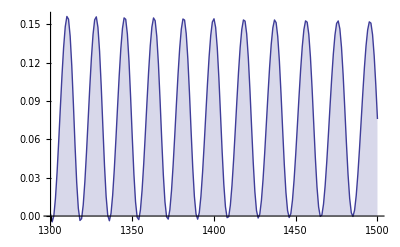

```mathematica
DiscretePlot[Re@dl[n,N@Im@ZetaZero@101+.2I,2],{n,1300,1500}]
```